```mathematica
backgroundsolution[args_]:= Module[
{startI = 0,
endI = 100,
ϕcosmological = 0,
k = 16 Pi^2},
Shooter = args[[2]];
ϕ0 = args[[1]];
backgroundsolutioninterior= NDSolve[{D[u[r,t],r,r] == -k D[u[r,t],t,t],u[r,0] ==Sin[r] √k,u[startI,t] ==  ϕ0},
u,{r,startI,endI},{t,startI,endI}];
Proximity= (u[endI,endI]/.backgroundsolutioninterior) -ϕcosmological;
If[Shooter,Prepend[Proximity,ϕ0],backgroundsolutioninterior]
]
```

```mathematica
solutions = Parallelize[Table[backgroundsolution[{x,True}],{x,Range[10000,1000000,10000]}]];
```

```mathematica
solutions;
```

```mathematica
solutions = Table[backgroundsolution[{x,True}],{x,Range[-1,2,.01]}];
```

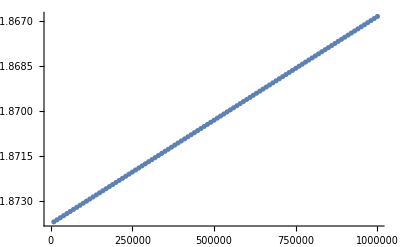

```mathematica
ListPlot[solutions]
```

```mathematica
sol = backgroundsolution[{0,False}]
```

{{u→InterpolatingFunction[…]}}

```mathematica
Plot3D[u[r,t]/.sol,{r,0,100},{t,0,100},AxesLabel->Automatic]
```

-Graphics3D-

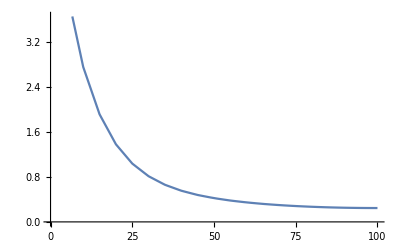

```mathematica
Plot[u[1,t]/.sol,{t,0,100}]
```

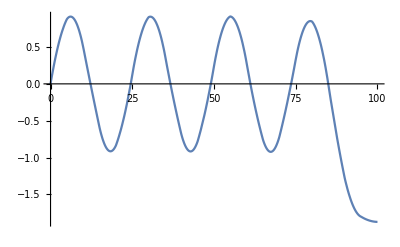

```mathematica
Plot[u[r,100]/.sol,{r,0,100}]
```